```mathematica
(***********************************************************************)
(*Постановка задачи*)
(***********************************************************************)
```

```mathematica
(*Количество опор*)
n=6;

(*Вершины октаэдра с заданным радиусом описанной сферы*)
octaPoint={{-#,0,0},{0,-#,0},{0,0,-#},{#,0,0},{0,#,0},{0,0,#}}&;

(*Координаты внешних (O) и внутренних (I) точек опор в системе координат, связанной с корпусом*)
Op=octaPoint[R];
Ip`o=octaPoint[r];

(*Координаты центра тяжести рабочего органа*)
position={x,y,z};

(*Кватернин вращения на угол theta относительно оси, заданной сферическими координатами alpha и omega*)
q={Cos[theta],Sin[theta]*Cos[alpha]*Cos[omega],Sin[theta]*Sin[alpha]*Cos[omega],Sin[theta]*Sin[omega]};

(*Поворот вектора #1 с помощью кватерниона #2*)
rotateWithQuaternion=
{(#1[[1]]*(1-2*#2[[3]]^2-2*#2[[4]]^2)+#1[[2]]*2*(#2[[2]]*#2[[3]]+#2[[1]]*#2[[4]])+#1[[3]]*2*(#2[[2]]*#2[[4]]-#2[[1]]*#2[[3]])),
(#1[[1]]*2*(#2[[2]]*#2[[3]]-#2[[1]]*#2[[4]])+#1[[2]]*(1-2*#2[[2]]^2-2*#2[[4]]^2)+#1[[3]]*2*(#2[[3]]*#2[[4]]+#2[[1]]*#2[[2]])),
(#1[[1]]*2*(#2[[2]]*#2[[4]]+#2[[1]]*#2[[3]])+#1[[2]]*2*(#2[[3]]*#2[[4]]-#2[[1]]*#2[[2]])+#1[[3]]*(1-2*#2[[2]]^2-2*#2[[3]]^2))}&;

(*Координаты универсальных шарниров смещенного рабочего органа*)
Ip=(position+rotateWithQuaternion[#,q])&/@Ip`o;

(*Квадрат расстояния между векторами*)
SqDistance3D=((#1[[1]]-#2[[1]])^2+(#1[[2]]-#2[[2]])^2+(#1[[3]]-#2[[3]])^2)&;

(*Система уравнений прямой и обратной кинематической задачи осесимметричного способа ограничения степеней подвижности рабочего органа*)
L=Symbol["L"<>ToString[#]]&;

lhs=(SqDistance3D[Op[[#]],Ip[[#]]]-L[#]^2)&/@Range[3];
assumptions={theta->0,alpha->0,omega->0};
equations=Thread[lhs==ConstantArray[0,3]]/.assumptions
```

{-L1^2+(r-R-x)^2+y^2+z^2==0,-L2^2+x^2+(r-R-y)^2+z^2==0,-L3^2+x^2+y^2+(r-R-z)^2==0}

```mathematica
(***********************************************************************)
(*Аналитическое решение задачи*)
(***********************************************************************)
```

```mathematica
(*Символьное решение системы уравнений обратной кинемтической задачи*)
L`l=L/@Range[3];
solution`inverse=Solve[equations,L`l];
solution`inverse=FullSimplify[Last[solution`inverse]]

(*Символьное решение системы уравнений прямой кинемтической задачи*)
solution`forward=Solve[equations,position];
solution`forward=FullSimplify[Last[solution`forward]]

(*Символьное выражение скорости перемещения центра тяжести*)
dLdt=Symbol["dL"<>ToString[#]<>"dt"]&;
dLdt`l=dLdt/@Range[3];
velocity={dxdt,dydt,dzdt};
solution`inverse`velocity=FullSimplify[Dt[solution`inverse,t,Constants->{R,r}]]/.Join[(Dt[#[[1]],t,Constants->{r,R}]->#[[2]])&/@Transpose[{Join[position,L`l],Join[velocity,dLdt`l]}]]

(*Символьное выражение ускорения перемещения центра тяжести*)
d2Ldt2=Symbol["d2L"<>ToString[#]<>"dt2"]&;
d2Ldt2`l=d2Ldt2/@Range[3];
acceleration={d2xdt2,d2ydt2,d2zdt2};
solution`inverse`acceleration=FullSimplify[Dt[solution`inverse`velocity,t,Constants->{R,r}]]/.Join[(Dt[#[[1]],t,Constants->{r,R}]->#[[2]])&/@Transpose[{Join[position,velocity,L`l,dLdt`l],Join[velocity,acceleration,dLdt`l,d2Ldt2`l]}]]

(*Учет ограничения скорости изменения длины опор*)
CylindricalDecomposition[Thread[dLdt`l^2<=ConstantArray[maxLvelocity^2,3]]/.solution`inverse`velocity,velocity]
```

{L1→√((-r+R+x)^2+y^2+z^2),L2→√(x^2+(-r+R+y)^2+z^2),L3→√(x^2+y^2+(-r+R+z)^2)}

{x→((-2 L1^2+L2^2+L3^2+2 (r-R)^2) (r-R)+√2 √(-(r-R)^2 (L1^4+L2^4+L3^4-2 L3^2 r^2+4 r^4-L2^2 (L3^2+2 (r-R)^2)-L1^2 (L2^2+L3^2+2 (r-R)^2)+4 r (L3^2-4 r^2) R-2 (L3^2-12 r^2) R^2-16 r R^3+4 R^4)))/(6 (r-R)^2),y→((L1^2-2 L2^2+L3^2+2 (r-R)^2) (r-R)+√2 √(-(r-R)^2 (L1^4+L2^4+L3^4-2 L3^2 r^2+4 r^4-L2^2 (L3^2+2 (r-R)^2)-L1^2 (L2^2+L3^2+2 (r-R)^2)+4 r (L3^2-4 r^2) R-2 (L3^2-12 r^2) R^2-16 r R^3+4 R^4)))/(6 (r-R)^2),z→(√2 √(-(r-R)^2 (L1^4+L2^4+L3^4-2 L3^2 r^2+4 r^4-L2^2 (L3^2+2 (r-R)^2)-L1^2 (L2^2+L3^2+2 (r-R)^2)+4 r (L3^2-4 r^2) R-2 (L3^2-12 r^2) R^2-16 r R^3+4 R^4))+(r-R) (L1^2+L2^2-2 (L3+r-R) (L3-r+R)))/(6 (r-R)^2)}

{dL1dt→(dxdt (-r+R+x)+dydt y+dzdt z)/(√((-r+R+x)^2+y^2+z^2)),dL2dt→(dxdt x+dydt (-r+R+y)+dzdt z)/(√(x^2+(-r+R+y)^2+z^2)),dL3dt→(dxdt x+dydt y+dzdt (-r+R+z))/(√(x^2+y^2+(-r+R+z)^2))}

{d2L1dt2→(-2 (dxdt (-r+R+x)+dydt y+dzdt z)^2+2 (dxdt^2+dydt^2+dzdt^2+d2xdt2 (-r+R+x)+d2ydt2 y+d2zdt2 z) ((-r+R+x)^2+y^2+z^2))/(2 ((-r+R+x)^2+y^2+z^2)^(3/2)),d2L2dt2→(-2 (dxdt x+dydt (-r+R+y)+dzdt z)^2+2 (dxdt^2+dydt^2+dzdt^2+d2xdt2 x+d2ydt2 (-r+R+y)+d2zdt2 z) (x^2+(-r+R+y)^2+z^2))/(2 (x^2+(-r+R+y)^2+z^2)^(3/2)),d2L3dt2→(-2 (dxdt x+dydt y+dzdt (-r+R+z))^2+2 (dxdt^2+dydt^2+dzdt^2+d2xdt2 x+d2ydt2 y+d2zdt2 (-r+R+z)) (x^2+y^2+(-r+R+z)^2))/(2 (x^2+y^2+(-r+R+z)^2)^(3/2))}

CylindricalDecomposition::nrtpi: {(dxdt (Times[«2»]+R+x)+dydt y+dzdt z)^2/((Times[«2»]+R+x)^2+y^2+z^2)≤maxLvelocity^2,(dxdt x+dydt (Times[«2»]+R+y)+dzdt z)^2/(x^2+(Times[«2»]+R+y)^2+z^2)≤maxLvelocity^2,(dxdt x+dydt y+dzdt (Times[«2»]+R+z))^2/(x^2+y^2+(Times[«2»]+R+z)^2)≤maxLvelocity^2} is not a logical formula consisting of polynomial equations and inequalities in {dxdt,dydt,dzdt} with rational number coefficients.

CylindricalDecomposition[{(dxdt (-r+R+x)+dydt y+dzdt z)^2/((-r+R+x)^2+y^2+z^2)≤maxLvelocity^2,(dxdt x+dydt (-r+R+y)+dzdt z)^2/(x^2+(-r+R+y)^2+z^2)≤maxLvelocity^2,(dxdt x+dydt y+dzdt (-r+R+z))^2/(x^2+y^2+(-r+R+z)^2)≤maxLvelocity^2},{dxdt,dydt,dzdt}]

```mathematica
(***********************************************************************)
(*Численное решение задачи*)
(***********************************************************************)
```

```mathematica
(*Конкретные значения параметров и координат сферических шарниров*)
parameters={R->1,r->1/3};

(*Начальные приближения неизвестных величин уравнений обратной и прямой кинематических задач для решения численным методом*)
L0=(R-r)/.parameters;
eps=0.001;
initialConditions`inverse={{L1,L0},{L2,L0},{L3,L0}};
initialConditions`forward={{x,#[[1]]},{y,#[[2]]},{z,#[[3]]}}&;

(*Сетка положений центра тяжести*)
delta=0.04;
maxvalue=(R-r)/.parameters;
maxvalue=Floor[maxvalue/delta]*delta;
range=Range[-maxvalue,maxvalue,delta];

(*Шарообразная область*)
grid=Select[Tuples[range,3],(Norm[#]<=(R-r)/.parameters)&];

(*Численное решение обратной кинематической задачи в области*)
calculator=FindRoot[#1/.Join[parameters,#2],#3,MaxIterations->100]&;

xyz={x->#[[1]],y->#[[2]],z->#[[3]]}&;
solutions=AssociationMap[calculator[equations,xyz[#],initialConditions`inverse]&,grid];

(*Численное решение прямой кинематической задачи в области для контроля точности решения обратной кинематической задачи*)
positions=AssociationMap[calculator[equations[[{1,2,3}]],solutions[#],initialConditions`forward[#]]&,grid];

(*Максимальная ошибка решения на сетке*)
error=Norm[Values[positions[#]]-#]/.parameters&;
sortedErrors=Sort[error/@grid,#1>#2&]

(*Конкретные значения координат точек*)
Op`v=Op/.parameters;
Ip`v=AssociationMap[Ip/.Join[parameters,xyz[#],solutions[#]]&,grid];

(*Длина четвертой, пятой и шестой опор*)
L4=AssociationMap[Sqrt[SquaredEuclideanDistance[Op`v[[4]],Ip`v[#][[4]]]]&,grid];
L5=AssociationMap[Sqrt[SquaredEuclideanDistance[Op`v[[5]],Ip`v[#][[5]]]]&,grid];
L6=AssociationMap[Sqrt[SquaredEuclideanDistance[Op`v[[6]],Ip`v[#][[6]]]]&,grid];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{5.31906×10^-14,4.80943×10^-14,4.66041×10^-14,3.87473×10^-14,3.87473×10^-14,3.84432×10^-14,2.52087×10^-14,2.50478×10^-14,2.38662×10^-14,2.36392×10^-14,2.33289×10^-14,2.33289×10^-14,2.08183×10^-14,2.08183×10^-14,2.07948×10^-14,2.07948×10^-14,2.06574×10^-14,2.06574×10^-14,1.40373×10^-14,1.40373×10^-14,1.40373×10^-14,1.40373×10^-14,1.35913×10^-14,1.33887×10^-14,1.33887×10^-14,1.29019×10^-14,1.18938×10^-14,1.18938×10^-14,1.16241×10^-14,1.15509×10^-14,1.15509×10^-14,1.13575×10^-14,19317,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}
 |  |  |  |

```mathematica
(***********************************************************************)
```

```mathematica
(*
(*Расчет максимального угла поворота в шарнирах для каждого положения*)
maximumAngleUniversal=Pi;
maximumAngleSpherpositional=Pi;
positionMaxJointsAngles=AssociationMap[{Max[Apply[VectorAngle]/@Transpose[{Op`v-Ip`v[#],Ip`v[#]-ConstantArray[#,n]}]],Max[Apply[VectorAngle]/@Transpose[{Op`v-Ip`v[#],Op`v}]]}&,grid];

(*Расчет минимальной и максимальной длин опор*)
minimumLegLength=0*R/.parameters;
maximumLegLength=2*R/.parameters;
positionMinMaxLegsLengths=AssociationMap[{Min[Lookup[solutions[#],L1],Lookup[solutions[#],L2],Lookup[solutions[#],L3],L4[#],L5[#],L6[#]],Max[Lookup[solutions[#],L1],Lookup[solutions[#],L2],Lookup[solutions[#],L3],L4[#],L5[#],L6[#]]}&,grid];

(*Определение допустимости положения*)
positionAdmissibility=AssociationMap[((positionMaxJointsAngles[#][[1]]<maximumAngleUniversal)&&(positionMaxJointsAngles[#][[2]]<maximumAngleSpherpositional)&&(positionMinMaxLegsLengths[#][[1]]>=minimumLegLength)&&(positionMinMaxLegsLengths[#][[2]]<=maximumLegLength))&,grid];
*)
```

```mathematica
(***********************************************************************)
```

```mathematica
(*
(*Изображение полной рабочей зоны*)
nearestpoint=Nearest[Select[Keys[positionAdmissibility],(positionAdmissibility[#]&&(Norm[#]<=(R-r-delta)/.parameters))&]];
inRegion[pt:{_Real,_Real,_Real},eps_Real]:=TrueQ[SquaredEuclideanDistance[nearestpoint[pt,1][[1]],pt]<eps^2];
Show[{RegionPlot3D[inRegion[{x,y,z},delta],{x,-maxvalue,maxvalue},{y,-maxvalue,maxvalue},{z,-maxvalue,maxvalue},Mesh->False,PlotPoints->40],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},R/.parameters]}]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic]

(*Расчет максимального радиуса шарообразной области рабочей зоны*)
inadmissiblePoints=Select[Keys[positionAdmissibility],Not[positionAdmissibility[#]]&];
working`radius=If[Length[inadmissiblePoints]==0,(R-r)/.parameters,Norm[Nearest[inadmissiblePoints,{0,0,0}]]]
*)
working`radius=1/Sqrt[6]*R/.parameters;
working`radius//N

(*Изображение максимальной шарообразной рабочей зоны*)
Show[{Graphics3D[{Yellow,Opacity[1],Sphere[{0,0,0},working`radius]}],Graphics3D[{Opacity[0.5],Sphere[{0,0,0},R/.parameters]}]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic]
```

0.408248

-Graphics3D-

```mathematica
(***********************************************************************)
```

```mathematica
(*Интерактивная демонстрация положения рабочего органа*)
blackline={Thick,Line[#]}&;
redline={Thick,Red,Line[#]}&;

Dynamic@updatedVxyz
(*Dynamic@updatedVadmissibility*)
Manipulate[
updatedVxyz={{x,y,z},Norm[{x,y,z}]};
(*updatedVadmissibility={positionAdmissibility[{x,y,z}],N[positionMaxJointsAngles[{x,y,z}]/Pi*180],positionMinMaxLegsLengths[{x,y,z}]};*)
If[Norm[{x,y,z}]≤(R-r)/.parameters,
Ip`vv=Ip`v[{x,y,z}]/.assumptions;
Op`vv=Op`v/.assumptions;
Show[{ListPointPlot3D[{Ip`vv,Op`v},PlotStyle->{{Yellow,PointSize[Large]},{Green,PointSize[Large]}}],Graphics3D[blackline/@({Ip`vv[[#[[1]]]],Ip`vv[[#[[2]]]]}&/@Select[Subsets[Range[n],{2}],(Abs[#[[1]]-#[[2]]]!=3)&])],
Graphics3D[redline/@({Op`v[[#]],Ip`vv[[#]]}&/@Range[6])]},SphericalRegion->True,PlotRange->All,BoxRatios->Automatic],updatedVadmissibility={}],{{x,0.},range},{{y,0.},range},{{z,0.},range},ControlType->Slider]
```

Last::nolast: {} has zero length and no last element.

```mathematica
(***********************************************************************)
```

0.388808

{{0,3.81421},{22.8803,0}}

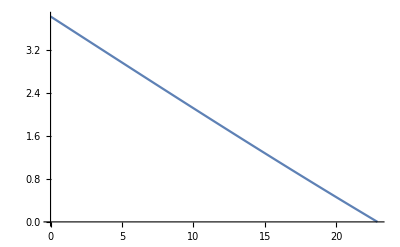

```mathematica
(*Максимальное отклонение центра тяжести робота-сферы*)
g=9.81; (*м/с^2*)
propToSphereRelativeMass=20; (*кг/кг*)
CG=working`radius*(propToSphereRelativeMass/(propToSphereRelativeMass+1)); (*м*)
N[CG]

(*Максимальный угол уклона поверхности*)
maxRamp=N[(ArcSin[CG/R]/Pi*180)/.parameters];

(*Максимальное ускорение в зависимости от уклона поверхности*)
acceleration=((CG-R*Sin[phi*Pi/180])*g/R)/.parameters;(*м/с^2*)

{{0,acceleration/.phi->0},{maxRamp,0}}
Plot[acceleration,{phi,0,maxRamp}]
```

```mathematica
(***********************************************************************)
```